## A reanalysis of the SH0ES data for H_0. Hints for a transition in the SnIa absolute luminosity and magnitude M_B

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb,NMinimize::cvmit,NIntegrate::slwcon,FindMinimum::lstol,General::luc];
```

## Pantheon data with Inverse Distance Ladder (IDL) H_0

### Various Constants

```mathematica
(* Riess' measurement - See arxiv:1903.07603 *)
h0r=0.74;
(* Planck18 Values *)
h0c=0.674; 
om0=0.31; 
(* Other Constants *)
c=299792.458;
cH0=2997.92458;
Tcmb=2.7255;
```

#### Full Pantheon χ^2

```mathematica
(* Import the Full Pantheon Data *)
dataPanth=Import[".\\data\\lcparam_DS17f.txt","Table"];
ndatPanth=Length[dataPanth]-1;
Dij0=Import[".\\data\\sys_DS17f.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Id=ConstantArray[1,ndatPanth];
(* Statistical Uncertainties *)
Covstat=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2];
(* Systematic Uncertainties *)
Covsys=Dij;
Cijtot=Covsys+Covstat;
InvCovTotal=Inverse[Cijtot];
InvCovstat=Inverse[Covstat];
```

```mathematica
(* Equivalent form of the LwPT Dark Energy Model as a function of α *)
w[a_,w0_,wa_,at_]:=w0+wa HeavisideTheta[1/a -1 /at]
(* Subscript[f, DE](α) for LwPT Dark Energy Model *)
f[a_,w0_,wa_,at_]:=ⅇ^(-3 ((1+w0) Log[a]+wa HeavisideTheta[1/a-1/at] Log[a/at]));
(* See Eq. (2) of arxiv:9709112 *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
H[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f[a,w0,wa,at]]
(* Sound speed *) 
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=(DLsol[om,w0,wa,h,at]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,w0,wa,h,at]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=(c/(100h)dL[z]/.DLsol[om,w0,wa,h,at])[[1]]//Chop
```

```mathematica
errall=Sqrt[Diagonal[Cijtot]];
```

```mathematica
listzt0=Table[{dataPanth[[1+i,2]],dataPanth[[1+i,5]]-Around[(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DL[dataPanth[[1+i,2]],om0,-1,0,h0c,1]]+25),errall[[i]]]},{i,1,ndatPanth}]
```

{{0.014,-19.420.04},{0.0194,-19.480.04},{0.0264,-19.4580.027},{0.0329,-19.4590.028},{0.0396,-19.4570.035},{0.0475,-19.470.04},{0.056,-19.500.04},{0.064,-19.460.05},{0.0721,-19.470.04},{0.0811,-19.360.05},{0.0889,-19.420.04},{0.1001,-19.360.04},{0.1071,-19.3830.035},{0.1195,-19.4390.027},{0.1278,-19.4120.029},{0.1396,-19.3570.025},{0.1519,-19.4310.026},{0.1635,-19.4870.028},{0.1778,-19.4130.022},{0.1906,-19.4140.023},{0.2067,-19.4300.024},{0.2216,-19.4240.025},{0.2405,-19.4330.024},{0.2558,-19.4330.021},{0.2762,-19.4630.023},{0.2972,-19.4300.023},{0.3215,-19.3930.022},{0.3453,-19.4200.025},{0.3708,-19.4240.025},{0.4049,-19.4120.033},{0.4355,-19.4210.029},{0.4738,-19.3990.030},{0.5174,-19.4240.032},{0.5742,-19.3970.028},{0.6299,-19.440.04},{0.724,-19.4420.031},{0.821,-19.3980.033},{0.9511,-19.390.04},{1.2336,-19.430.08},{1.6123,-19.520.10}}

```mathematica
Mprior=-19.253;
σMprior=0.0375;
```

```mathematica
hs[x_,k_]:=1/(1+Exp[-2k x])
mbf[mb1_,mb2_,x_,k_]:=mb1+(mb2-mb1) hs[x,k]
```

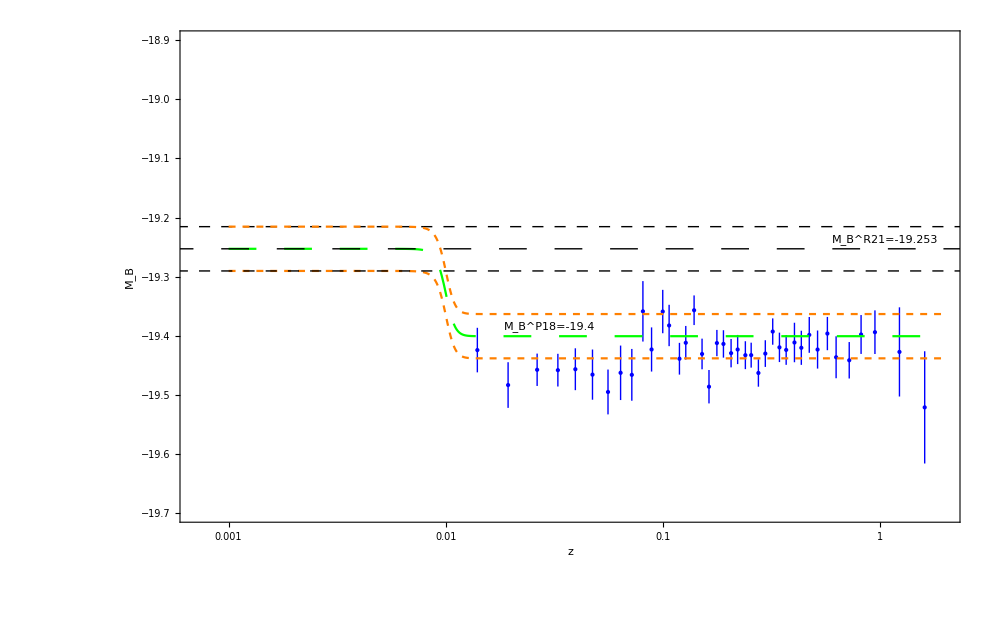

```mathematica
plt0=ListLogLinearPlot[{listzt0}, Frame->True,FrameLabel->{"z","M_B"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Blue},{PointSize->Large,Red},{PointSize->Large,RGBColor[0,0.32,0]}},ImageSize->1000, PlotRange->{{0.0007,2},{-19.7,-18.9}}, FrameStyle -> Directive[Black, Thick],Epilog->{Text["M_B^R21=-19.253",{0.06,-19.238}],Text["M_B^P18=-19.4",{-3.5,-19.385}],{Dashing[0.02],Line[{{-30,Mprior},{8,Mprior}}]},{Dashing[0.008],Line[{{-30,Mprior-σMprior},{8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{-30,Mprior+σMprior},{8,Mprior+σMprior}}]}}];
plt0b=ListLogLinearPlot[{listzt0}, Frame->{{False,True},{True,True}},FrameLabel->{"z","M_B"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Blue},{PointSize->Large,Red},{PointSize->Large,RGBColor[0,0.32,0]}},ImageSize->1000, PlotRange->{{0.0007,2},{-19.7,-18.9}}, FrameStyle -> Directive[Black, Thick],Epilog->{Text["M_B^R21=-19.253",{0.06,-19.238}],Text["M_B^P18=-19.4",{-3.5,-19.385}],{Dashing[0.02],Line[{{-30,Mprior},{8,Mprior}}]},{Dashing[0.008],Line[{{-30,Mprior-σMprior},{8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{-30,Mprior+σMprior},{8,Mprior+σMprior}}]}}];
Mprioru=Mprior+σMprior;
Mpriorbf=Mprior;
Mpriord=Mprior-σMprior;
dm=19.401-19.253;
zt=0.01;
dz=1/1000;
zmin=0.001;
zmax=2;
plm=LogLinearPlot[{mbf[Mprioru,Mprioru-dm,(z-zt),1/dz],mbf[Mpriorbf,Mpriorbf-dm,(z-zt),1/dz],mbf[Mpriord,Mpriord-dm,(z-zt),1/dz]},{z,zmin,zmax},PlotStyle->{{Dashed,Orange},{Dashing[0.02],Green}}];
Mbplot=Show[plt0,plm]
```

## Measured apparent magnitudes of the SnIa - Error Matrix C

```mathematica
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];
```

```mathematica
galc=Take[cdata[[1]]//Normal,{3131,3207},{3131,3207}];
```

```mathematica
sigmambsn[galc_]:=Table[Sqrt[galc[[i,i]]],{i,1,77}];
```

```mathematica
mbsner=sigmambsn[galc]
```

{0.119134,0.130076,0.113629,0.111935,0.111644,0.149243,0.0980847,0.208226,0.113535,0.166222,0.141873,0.0964822,0.0985703,0.15902,0.106571,0.149879,0.218862,0.0890211,0.103787,0.169783,0.105575,0.0798578,0.0944482,0.0797204,0.173964,0.119503,0.209143,0.147913,0.163861,0.0927015,0.0762945,0.0836754,0.138406,0.0992663,0.0980957,0.0966374,0.0861488,0.108111,0.123052,0.200809,0.236181,0.137851,0.130412,0.218675,0.0731994,0.0854854,0.119718,0.0861789,0.0877198,0.148295,0.0863887,0.105516,0.135883,0.0943167,0.0937831,0.0890736,0.221629,0.161867,0.118377,0.111783,0.161009,0.132982,0.0963932,0.14249,0.104227,0.181935,0.210458,0.0841251,0.132317,0.132391,0.0949779,0.144772,0.122682,0.106198,0.103034,0.100917,0.101942}

```mathematica
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"] [[1]]//Normal;
```

```mathematica
mbsn=Take[ydata//Normal,{3131,3207}]
```

{9.752,9.808,13.646,13.648,13.67,13.602,13.499,13.124,13.427,15.214,15.287,13.22,13.198,11.885,11.915,12.254,11.752,12.148,12.133,12.198,12.271,12.822,12.667,12.695,13.443,13.114,13.936,13.821,13.843,13.188,13.215,12.937,12.684,12.787,13.509,12.548,12.252,12.434,12.383,11.478,11.496,11.551,12.454,13.173,13.986,14.001,13.792,13.969,12.822,12.754,12.852,12.787,11.214,11.29,11.15,11.265,13.394,13.494,13.655,12.949,12.928,12.958,13.074,13.085,13.077,12.254,12.313,14.03,13.467,13.369,14.047,14.134,14.274,14.227,13.551,13.499,13.525}

## The means of the measured apparent magnitudes of the SnIa

```mathematica
l=0;
```

```mathematica
k=1;
```

```mathematica
g=1;
```

```mathematica
tablemb={};
Do[
chi2[z_?NumberQ]:=Sum[((mbsn[[i]]-z)/Sqrt[mbsner[[i]]^2])^2,{i,k+l,n}];
chi2min=FindMinimum[chi2[z],{z,mbsn[[n]]}];
s1=FindRoot[chi2[w]==chi2min[[1]]+1,{w,chi2min[[2,1,2]]+0.5}][[1,2]]-chi2min[[2,1,2]];
l=n;
g=g+1;
AppendTo[tablemb,{chi2min[[2,1,2]],s1}],{n,{2,5,6,9,11,13,15,17,19,21,24,25,26,29,31,32,34,35,36,37,39,41,42,43,44,48,52,56,59,62,65,67,68,70,72,74,77}}]
```

```mathematica
tablemb
```

{{9.77755,0.0878548},{13.6548,0.06489},{13.602,0.149243},{13.4294,0.0699137},{15.2562,0.107912},{13.2092,0.0689497},{11.9057,0.088529},{12.0937,0.123662},{12.1416,0.0675702},{12.2506,0.0896555},{12.7344,0.0484357},{13.443,0.173964},{13.114,0.119503},{13.8536,0.0972146},{13.2041,0.0589091},{12.937,0.0836754},{12.752,0.0806646},{13.509,0.0980957},{12.548,0.0966374},{12.252,0.0861488},{12.4118,0.0812177},{11.4856,0.152987},{11.551,0.137851},{12.454,0.130412},{13.173,0.218675},{13.9599,0.043524},{12.8164,0.0500475},{11.2329,0.0496103},{13.5668,0.087744},{12.9473,0.0755603},{13.0773,0.0633815},{12.2792,0.137636},{14.03,0.0841251},{13.418,0.0935886},{14.0732,0.0794134},{14.2471,0.0802937},{13.5246,0.0588629}}

## SH0ES data with baseline model (37 hosts, no IDL constraint)

```mathematica
Y=ydata;(* This is the matrix of measurements*)
```

```mathematica
(* The system is Y=L qpar. qpar has single column with 47 entries. Entry 45 is useless and does not appear anywhere but we keep it for completeness as it has been included in the fits data but it is not mentioned in Riess 21. *)
```

```mathematica
qpar={"mu_{M101}","mu_{M1337}","mu_{N0691}","mu_{N1015}","mu_{N0105}","mu_{N1309}","mu_{N1365}","mu_{N1448}","mu_{N1559}","mu_{N2442}","mu_{N2525}","mu_{N2608}","mu_{N3021}","mu_{N3147}","mu_{N3254}","mu_{N3370}","mu_{N3447}","mu_{N3583}","mu_{N3972}","mu_{N3982}","mu_{N4038}","mu_{N4424}","mu_{N4536}","mu_{N4639}","mu_{N4680}","mu_{N5468}","mu_{N5584}","mu_{N5643}","mu_{N5728}","mu_{N5861}","mu_{N5917}","mu_{N7250}","mu_{N7329}","mu_{N7541}","mu_{N7678}","mu_{N0976}","mu_{U9391}","Delta mu_{Ν4258}","M_H^W","Delta mu_{LMC}","mu_{M31}","b_W","M_B","Z_W","X","Delta zp","5 log H_0"}; 
(* The length of the parameter vector is longer than expected due to an extra parameter X that has benn included but play no role at all and is not mentioned in their paper. The expected length is 46. *)
```

```mathematica
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
```

```mathematica
trL=ldata[[1,2]]//Normal;
```

```mathematica
L=Transpose[trL](* Y = L.qpar . L denotes the original model used by the SH0ES team*);
```

```mathematica
Call=cdata[[1]]//Normal;(* This is the Covariance matrix*)
```

```mathematica
InvCall=Inverse[Call];
```

```mathematica
sigma=Inverse[trL.InvCall.L];
```

```mathematica
(* These are the best fit parameter values. These formulas are proven in https://people.duke.edu/~hpgavin/SystemID/CourseNotes/linear-least-squres.pdf eq. 11 *)
```

```mathematica
qbf=sigma.(trL.InvCall.Y)
```

{29.1596,32.9156,32.8222,32.6178,34.4934,32.509,31.3254,31.2951,31.4608,31.4652,32.0114,32.6278,32.3916,33.0908,32.4031,32.1425,31.9443,32.7899,31.7072,31.6382,31.6338,30.8239,30.8355,31.7874,32.5468,33.1873,31.8655,30.5084,32.9159,32.2052,32.3369,31.606,33.2692,32.5797,33.2669,33.5439,32.816,-0.0127018,-5.89352,0.0100843,24.3714,-0.0135244,-19.2529,-0.216585,0.,-0.0738103,9.31789}

```mathematica
(* the  1 sigma errors for the  parameters *)
```

```mathematica
sigmadiag=Table[Sqrt[sigma[[i,i]]],{i,1,47}]
```

{0.0387512,0.0821192,0.0876812,0.0600767,0.119358,0.050678,0.0500633,0.0357285,0.0516334,0.0546367,0.0606591,0.114843,0.096619,0.085483,0.0564277,0.0456347,0.0333316,0.0634223,0.0676238,0.0561344,0.0800615,0.108035,0.0479758,0.0713565,0.147044,0.0485086,0.0453757,0.0423385,0.103193,0.0756345,0.0769425,0.103313,0.070201,0.0843556,0.0832043,0.0823285,0.0544389,0.0217961,0.0180529,0.0194059,0.0686838,0.0149153,0.0288987,0.0452084,0.0000316228,0.0105856,0.0299413}

```mathematica
(* the  redshifts of the 37 galaxies*)
```

```mathematica
reds={0.0008,0.00853,0.00889,0.00877,0.01765,0.00713,0.00546,0.00390,0.00435,0.00489,0.00527,0.00719,0.00512,0.00935,0.00452,0.00427,0.00356,0.00702,0.00284,0.00371,0.00542,0.00146,0.00603,0.00340,0.00831,0.00948,0.00546,0.00400,0.00932,0.00617,0.00638,0.00389,0.01085,0.00898,0.01164,0.01433,0.00635};
```

```mathematica
res1=Table[{qpar[[i]],reds[[i]],Round[qbf[[i]],0.01],Round[sigmadiag[[i]],0.01]},{i,1,37}]
```

{{mu_{M101},0.0008,29.16,0.04},{mu_{M1337},0.00853,32.92,0.08},{mu_{N0691},0.00889,32.82,0.09},{mu_{N1015},0.00877,32.62,0.06},{mu_{N0105},0.01765,34.49,0.12},{mu_{N1309},0.00713,32.51,0.05},{mu_{N1365},0.00546,31.33,0.05},{mu_{N1448},0.0039,31.3,0.04},{mu_{N1559},0.00435,31.46,0.05},{mu_{N2442},0.00489,31.47,0.05},{mu_{N2525},0.00527,32.01,0.06},{mu_{N2608},0.00719,32.63,0.11},{mu_{N3021},0.00512,32.39,0.1},{mu_{N3147},0.00935,33.09,0.09},{mu_{N3254},0.00452,32.4,0.06},{mu_{N3370},0.00427,32.14,0.05},{mu_{N3447},0.00356,31.94,0.03},{mu_{N3583},0.00702,32.79,0.06},{mu_{N3972},0.00284,31.71,0.07},{mu_{N3982},0.00371,31.64,0.06},{mu_{N4038},0.00542,31.63,0.08},{mu_{N4424},0.00146,30.82,0.11},{mu_{N4536},0.00603,30.84,0.05},{mu_{N4639},0.0034,31.79,0.07},{mu_{N4680},0.00831,32.55,0.15},{mu_{N5468},0.00948,33.19,0.05},{mu_{N5584},0.00546,31.87,0.05},{mu_{N5643},0.004,30.51,0.04},{mu_{N5728},0.00932,32.92,0.1},{mu_{N5861},0.00617,32.21,0.08},{mu_{N5917},0.00638,32.34,0.08},{mu_{N7250},0.00389,31.61,0.1},{mu_{N7329},0.01085,33.27,0.07},{mu_{N7541},0.00898,32.58,0.08},{mu_{N7678},0.01164,33.27,0.08},{mu_{N0976},0.01433,33.54,0.08},{mu_{U9391},0.00635,32.82,0.05}}

## SH0ES data with M_B transition dof (37 hosts, no IDL constraint)

```mathematica
distall=Import[".\\data\\distall.txt","Table"];
dist1=distall[[All,1]];
dof=3446;
NN=3492;
MM=48;

col=47-4; (* this column corresponds to the parameter to be split (e.g. for MB  we have col=43 *)
qpar={"mu_{M101}","mu_{M1337}","mu_{N0691}","mu_{N1015}","mu_{N0105}","mu_{N1309}","mu_{N1365}","mu_{N1448}","mu_{N1559}","mu_{N2442}","mu_{N2525}","mu_{N2608}","mu_{N3021}","mu_{N3147}","mu_{N3254}","mu_{N3370}","mu_{N3447}","mu_{N3583}","mu_{N3972}","mu_{N3982}","mu_{N4038}","mu_{N4424}","mu_{N4536}","mu_{N4639}","mu_{N4680}","mu_{N5468}","mu_{N5584}","mu_{N5643}","mu_{N5728}","mu_{N5861}","mu_{N5917}","mu_{N7250}","mu_{N7329}","mu_{N7541}","mu_{N7678}","mu_{N0976}","mu_{U9391}","Delta mu_{Ν4258}","M_H^W","Delta mu_{LMC}","mu_{M31}","b_W","M_B1","M_B2","Z_W","X","Delta zp","5 log H_0"}; 
(* introduce here the names of the two new parameters that replace the previous parameter *)
percol1=L[[All,col]]//Normal; (* construct two columns from the Subscript[M, B] column of L with nearby and distant objects *)
Dcrit=50;
percol1s=percol1;
percol1l=percol1;
Do[
If[dist1[[i]]≥ Dcrit,percol1s[[i]]=0]; (* in the nearby Subscript[M, B,s] column put 0 in the distant elements ie those that are beyond dcrit *)
If[0<=dist1[[i]]< Dcrit,percol1l[[i]]=0] (* in the distant Subscript[M, B,l] column put 0 in the nearby elements ie those that are closer than dcrit. Elements with negative distance are ignored. *)
,{i,1,Length[dist1]}];
trL1=Drop[trL,{col}] ;(* Remove the MB column of L to replace it with two other columns for the nearby and distant parameters (Subscript[M, B,s] and Subscript[M, B,l]) *)
trL2=Insert[Insert[trL1,percol1s,col],percol1l,col+1] ;(* Replace with the new columns *)
Lnew=Transpose[trL2]; (* this is the model matrix Lnew for the new model with one new parameter *)
trLnew=trL2 ;(* The system is Y=L qpar. qpar has single column with 47 entries. Entry 45 is useless and does not appear anywhere but we keep it for completeness as it has been included in the fits data but it is not mentioned in Riess 21. *);
sigma=Inverse[trLnew.InvCall.Lnew];
qbf=sigma.(trLnew.InvCall.Y) (* These are the best fit parameter values. These formulas are proven in https://people.duke.edu/~hpgavin/SystemID/CourseNotes/linear-least-squres.pdf eq. 11 *)
```

{29.1595,32.9135,32.8207,32.6166,34.6314,32.5079,31.3249,31.2948,31.4598,31.4635,32.0094,32.6259,32.3892,33.0883,32.4014,32.1417,31.9439,32.7883,31.7055,31.637,31.6315,30.8231,30.8351,31.7864,32.5456,33.1854,31.8642,30.5071,32.913,32.2031,32.3345,31.6048,33.2673,32.5774,33.264,33.6707,32.8148,-0.0127257,-5.89364,0.00995554,24.3714,-0.0133474,-19.2495,-19.43,-0.217325,0.,-0.0738192,9.14091}

```mathematica
(* the best fit papameter values with 1 sigma errors for H0 and for the two new parameters *)
h0=10^(qbf[[48]]/5) (* We obtain the correct value of h0 since qbf[[47]]= 5 log Subscript[H, 0] *)
```

67.3259

```mathematica
dqbf48=Sqrt[sigma[[48,48]]]
dh0=Log[10] h0 dqbf48/5
```

0.149868

4.64662

```mathematica
(* the  1 sigma errors for the  parameters *)
sigmadiag=Table[Sqrt[sigma[[i,i]]],{i,1,48}]
```

{0.0387513,0.0821369,0.0876909,0.0600846,0.165407,0.0506861,0.0500654,0.03573,0.0516404,0.0546564,0.0606828,0.114854,0.0966392,0.0855087,0.0564454,0.0456403,0.0333333,0.0634368,0.0676394,0.0561436,0.0800842,0.108038,0.0479773,0.0713616,0.147048,0.0485345,0.0453889,0.0423517,0.103222,0.0756549,0.0769694,0.103318,0.0702183,0.0843778,0.0832405,0.133652,0.0544488,0.0217961,0.0180532,0.0194062,0.0686838,0.0149161,0.0290368,0.149761,0.0452126,0.0000316228,0.0105856,0.149868}

```mathematica
(* table of results for the 37 galaxies *)
restr50no=Table[{qpar[[i]],reds[[i]],Round[qbf[[i]],0.01],Round[sigmadiag[[i]],0.01]},{i,1,37}]
```

{{mu_{M101},0.0008,29.16,0.04},{mu_{M1337},0.00853,32.91,0.08},{mu_{N0691},0.00889,32.82,0.09},{mu_{N1015},0.00877,32.62,0.06},{mu_{N0105},0.01765,34.63,0.17},{mu_{N1309},0.00713,32.51,0.05},{mu_{N1365},0.00546,31.32,0.05},{mu_{N1448},0.0039,31.29,0.04},{mu_{N1559},0.00435,31.46,0.05},{mu_{N2442},0.00489,31.46,0.05},{mu_{N2525},0.00527,32.01,0.06},{mu_{N2608},0.00719,32.63,0.11},{mu_{N3021},0.00512,32.39,0.1},{mu_{N3147},0.00935,33.09,0.09},{mu_{N3254},0.00452,32.4,0.06},{mu_{N3370},0.00427,32.14,0.05},{mu_{N3447},0.00356,31.94,0.03},{mu_{N3583},0.00702,32.79,0.06},{mu_{N3972},0.00284,31.71,0.07},{mu_{N3982},0.00371,31.64,0.06},{mu_{N4038},0.00542,31.63,0.08},{mu_{N4424},0.00146,30.82,0.11},{mu_{N4536},0.00603,30.84,0.05},{mu_{N4639},0.0034,31.79,0.07},{mu_{N4680},0.00831,32.55,0.15},{mu_{N5468},0.00948,33.19,0.05},{mu_{N5584},0.00546,31.86,0.05},{mu_{N5643},0.004,30.51,0.04},{mu_{N5728},0.00932,32.91,0.1},{mu_{N5861},0.00617,32.2,0.08},{mu_{N5917},0.00638,32.33,0.08},{mu_{N7250},0.00389,31.6,0.1},{mu_{N7329},0.01085,33.27,0.07},{mu_{N7541},0.00898,32.58,0.08},{mu_{N7678},0.01164,33.26,0.08},{mu_{N0976},0.01433,33.67,0.13},{mu_{U9391},0.00635,32.81,0.05}}

## Figures 16 and 17

```mathematica
Mbbas1[res1_,tablemb_]:=Table[{res1[[i,2]],Around[tablemb[[i,1]]-res1[[i,3]],Sqrt[tablemb[[i,2]]^2+res1[[i,4]]^2]]},{i,1,37}]
```

```mathematica
Mbbas1[res1,tablemb]
```

{{0.0008,-19.380.10},{0.00853,-19.270.10},{0.00889,-19.220.17},{0.00877,-19.190.09},{0.01765,-19.230.16},{0.00713,-19.300.09},{0.00546,-19.420.10},{0.0039,-19.210.13},{0.00435,-19.320.08},{0.00489,-19.220.10},{0.00527,-19.280.08},{0.00719,-19.190.21},{0.00512,-19.280.16},{0.00935,-19.240.13},{0.00452,-19.200.08},{0.00427,-19.200.10},{0.00356,-19.190.09},{0.00702,-19.280.11},{0.00284,-19.160.12},{0.00371,-19.390.10},{0.00542,-19.220.11},{0.00146,-19.330.19},{0.00603,-19.290.15},{0.0034,-19.340.15},{0.00831,-19.380.27},{0.00948,-19.230.07},{0.00546,-19.050.07},{0.004,-19.280.06},{0.00932,-19.350.13},{0.00617,-19.260.11},{0.00638,-19.260.10},{0.00389,-19.330.17},{0.01085,-19.240.11},{0.00898,-19.160.12},{0.01164,-19.200.11},{0.01433,-19.290.11},{0.00635,-19.300.08}}

```mathematica
Mbtra50no[restr50no_,tablemb_]:=Table[{restr50no[[i,2]],Around[tablemb[[i,1]]-restr50no[[i,3]],Sqrt[tablemb[[i,2]]^2+restr50no[[i,4]]^2]]},{i,1,37}]
```

```mathematica
Mbtra50no[restr50no,tablemb]
```

{{0.0008,-19.380.10},{0.00853,-19.260.10},{0.00889,-19.220.17},{0.00877,-19.190.09},{0.01765,-19.370.20},{0.00713,-19.300.09},{0.00546,-19.410.10},{0.0039,-19.200.13},{0.00435,-19.320.08},{0.00489,-19.210.10},{0.00527,-19.280.08},{0.00719,-19.190.21},{0.00512,-19.280.16},{0.00935,-19.240.13},{0.00452,-19.200.08},{0.00427,-19.200.10},{0.00356,-19.190.09},{0.00702,-19.280.11},{0.00284,-19.160.12},{0.00371,-19.390.10},{0.00542,-19.220.11},{0.00146,-19.330.19},{0.00603,-19.290.15},{0.0034,-19.340.15},{0.00831,-19.380.27},{0.00948,-19.230.07},{0.00546,-19.040.07},{0.004,-19.280.06},{0.00932,-19.340.13},{0.00617,-19.250.11},{0.00638,-19.250.10},{0.00389,-19.320.17},{0.01085,-19.240.11},{0.00898,-19.160.12},{0.01164,-19.190.11},{0.01433,-19.420.15},{0.00635,-19.290.08}}

```mathematica
plMbbas1=ListLogLinearPlot[{Mbbas1[res1,tablemb]}, Frame->True,FrameLabel->{"z","M_B"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Red},{PointSize->Large,Red},{PointSize->Large,Red}},ImageSize->1000, PlotRange->{{0.0007,2},{-19.7,-18.9}}, FrameStyle -> Directive[Black, Thick]];
```

```mathematica
plMbtra50no=ListLogLinearPlot[{Mbtra50no[restr50no,tablemb]},Frame->{{False,True},{True,True}},FrameLabel->{"z",""},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Darker[Green]},{PointSize->Large,Darker[Green]},{PointSize->Large,Darker[Green]}},ImageSize->1000, PlotRange->{{0.0007,2},{-19.7,-18.9}}, FrameStyle -> Directive[Black, Thick]];
```

```mathematica
figMbbas1=Show[plt0,plm,plMbbas1,Graphics[{Inset[-  "SH0ES data with baseline  model (37 hosts, no IDL constraint)", {-1.8,-19.07},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",18}]}],Graphics[{Inset[-  "Pantheon data with Inverse Distance Ladder (IDL) H_0", {-2.09,-19.0 },BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",18}]}]];
```

```mathematica
Export[NotebookDirectory[]<>"figMbbas1.pdf",figMbbas1,ImageResolution->1000];
```

```mathematica
figMbtra50no=Show[plt0b,plm,plMbtra50no,Graphics[{Inset[-  "SH0ES data with M_B transition dof (37 hosts, no IDL constraint)", {-1.72,-19.07},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",18}]}],Graphics[{Inset[-  "Pantheon data with Inverse Distance Ladder (IDL) H_0", {-2.09,-19.0},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",18}]}]];
```

```mathematica
Export[NotebookDirectory[]<>"figMbtra50no.pdf",figMbtra50no,ImageResolution->1000];
```

```mathematica
sortMbbas1=Sort[Mbbas1[res1,tablemb]]
```

{{0.0008,-19.380.10},{0.00146,-19.330.19},{0.00284,-19.160.12},{0.0034,-19.340.15},{0.00356,-19.190.09},{0.00371,-19.390.10},{0.00389,-19.330.17},{0.0039,-19.210.13},{0.004,-19.280.06},{0.00427,-19.200.10},{0.00435,-19.320.08},{0.00452,-19.200.08},{0.00489,-19.220.10},{0.00512,-19.280.16},{0.00527,-19.280.08},{0.00542,-19.220.11},{0.00546,-19.420.10},{0.00546,-19.050.07},{0.00603,-19.290.15},{0.00617,-19.260.11},{0.00635,-19.300.08},{0.00638,-19.260.10},{0.00702,-19.280.11},{0.00713,-19.300.09},{0.00719,-19.190.21},{0.00831,-19.380.27},{0.00853,-19.270.10},{0.00877,-19.190.09},{0.00889,-19.220.17},{0.00898,-19.160.12},{0.00932,-19.350.13},{0.00935,-19.240.13},{0.00948,-19.230.07},{0.01085,-19.240.11},{0.01164,-19.200.11},{0.01433,-19.290.11},{0.01765,-19.230.16}}

```mathematica
l=0;
```

```mathematica
k=1;
```

```mathematica
binMbbas1={};
Do[
meanb=Mean[Table[sortMbbas1[[i,2]],{i,k+l,n}]];
meanz=Mean[Table[sortMbbas1[[i,1]],{i,k+l,n}]];
l=n;
AppendTo[binMbbas1,{meanz,meanb}],{n,{5,10,15,20,25,30,35,37}}]
```

```mathematica
binMbbas1
```

{{0.002412,-19.280.06},{0.003954,-19.280.05},{0.00483,-19.260.05},{0.005708,-19.250.05},{0.006814,-19.270.06},{0.008696,-19.240.07},{0.010128,-19.250.05},{0.01599,-19.260.10}}

```mathematica
plMbbas1bin=ListLogLinearPlot[{binMbbas1}, Frame->True,FrameLabel->{"z","M_B"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Red},{PointSize->Large,Red},{PointSize->Large,RGBColor[0,0.32,0]}},ImageSize->1000, PlotRange->{{0.0007,2},{-19.7,-18.9}}, FrameStyle -> Directive[Black, Thick]];
```

```mathematica
sorttra50n0=Sort[Mbtra50no[restr50no,tablemb]]
```

{{0.0008,-19.380.10},{0.00146,-19.330.19},{0.00284,-19.160.12},{0.0034,-19.340.15},{0.00356,-19.190.09},{0.00371,-19.390.10},{0.00389,-19.320.17},{0.0039,-19.200.13},{0.004,-19.280.06},{0.00427,-19.200.10},{0.00435,-19.320.08},{0.00452,-19.200.08},{0.00489,-19.210.10},{0.00512,-19.280.16},{0.00527,-19.280.08},{0.00542,-19.220.11},{0.00546,-19.410.10},{0.00546,-19.040.07},{0.00603,-19.290.15},{0.00617,-19.250.11},{0.00635,-19.290.08},{0.00638,-19.250.10},{0.00702,-19.280.11},{0.00713,-19.300.09},{0.00719,-19.190.21},{0.00831,-19.380.27},{0.00853,-19.260.10},{0.00877,-19.190.09},{0.00889,-19.220.17},{0.00898,-19.160.12},{0.00932,-19.340.13},{0.00935,-19.240.13},{0.00948,-19.230.07},{0.01085,-19.240.11},{0.01164,-19.190.11},{0.01433,-19.420.15},{0.01765,-19.370.20}}

```mathematica
l=0;
```

```mathematica
k=1;
```

```mathematica
bintra50no={};
Do[
meanb=Mean[Table[sorttra50n0[[i,2]],{i,k+l,n}]];
meanz=Mean[Table[sorttra50n0[[i,1]],{i,k+l,n}]];
l=n;
AppendTo[bintra50no,{meanz,meanb}],{n,{5,10,15,20,25,30,35,37}}]
```

```mathematica
bintra50no
```

{{0.002412,-19.280.06},{0.003954,-19.280.05},{0.00483,-19.260.05},{0.005708,-19.240.05},{0.006814,-19.260.06},{0.008696,-19.240.07},{0.010128,-19.250.05},{0.01599,-19.400.13}}

```mathematica
plMbtra50nobin=ListLogLinearPlot[{bintra50no}, Frame->True,FrameLabel->{"z","M_B"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Darker[Green]},{PointSize->Large,Darker[Green]},{PointSize->Large,Darker[Green]}},ImageSize->1000, PlotRange->{{0.0007,2},{-19.7,-18.9}}, FrameStyle -> Directive[Black, Thick]];
```

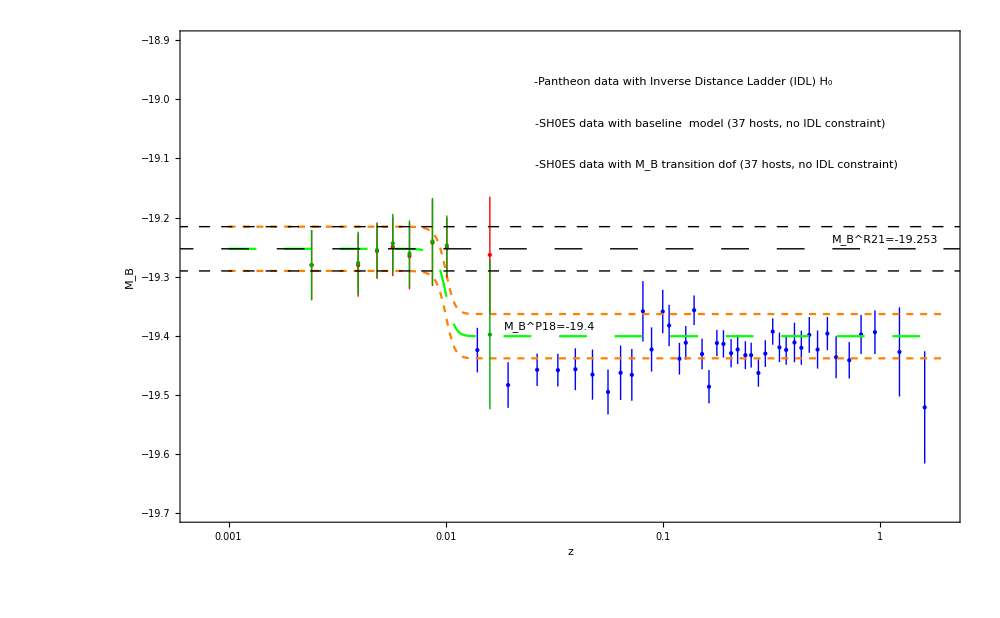

```mathematica
figMbbin=Show[plt0,plm,plMbbas1bin,plMbtra50nobin,Graphics[{Inset[-  "SH0ES data with baseline  model (37 hosts, no IDL constraint)", {-1.8,-19.04},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",18}]}],Graphics[{Inset[-  "SH0ES data with M_B transition dof (37 hosts, no IDL constraint)", {-1.73,-19.11},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",18}]}],Graphics[{Inset[-  "Pantheon data with Inverse Distance Ladder (IDL) H_0", {-2.08,-18.97},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",18}]}]]
```

```mathematica
Export[NotebookDirectory[]<>"figMbbin.pdf",figMbbin,ImageResolution->1000];
```

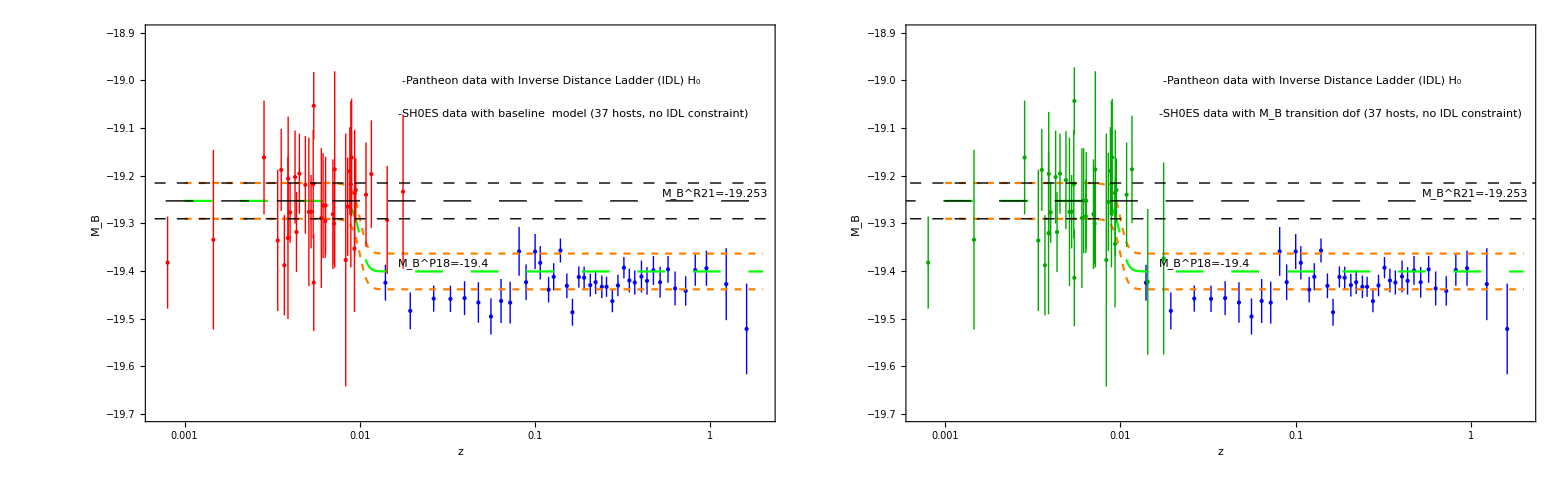

```mathematica
figMB2=GraphicsGrid[{{figMbbas1,figMbtra50no}},ImageSize->2000,Spacings->-58,AspectRatio->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"figMB2.pdf",figMB2,ImageResolution->1000];
```